Import the AtomicDensityMatrix package.  Available at http://rochesterscientific.com/ADM/.

```mathematica
<<AtomicDensityMatrix`
```

### Functions

Generate a table of the coupling coefficients between, and energy levels of, the ground (gs) and excited (es) magnetic sublevels in a field of strength B (where B is twice the Zeeman splitting of the ground F=1, mF=+/-1 subevels from the F=1,mF=0 sublevel.

```mathematica
CoeficientTable[gs_,es_,B_]:=Module[{d,h},
d=√2Table[WignerEckart[g,{Dipole,1,M[g]-M[e]},e]/.ReducedME[1,{Dipole,1},2]->1,{g,gs},{e,es}];
h=Hamiltonian[es,MagneticField->{0,0,B}]/.BohrMagneton->1;
TableForm[d.Eigenvectors[h]ᵀ,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs,es}}]]]

EnergyLevels[s_,B_]:=Module[{h},
h=Hamiltonian[s,MagneticField->{0,0,B}]/.BohrMagneton->1;
TableForm[Eigenvalues[h],TableHeadings->{Table[{F[i],M[i]},{i,s}]}]
]
```

These functions track the changing energy states and coupling values (as they are not returned in a consistent order from ADM).

```mathematica
SourceTargetCostMatrix[pointsA_,pointsB_,costFunction_:EuclideanDistance]:=Module[{lA=Length[pointsA],lB=Length[pointsB]},ArrayFlatten@{{0,ConstantArray[1,{1,lA}],ConstantArray[0,{1,lB}],0},{ConstantArray[0,{lA,1}],ConstantArray[0,{lA,lA}],Outer[costFunction,pointsA,pointsB,1],ConstantArray[0,{lA,1}]},{ConstantArray[0,{lB,1}],ConstantArray[0,{lB,lA}],ConstantArray[0,{lB,lB}],ConstantArray[1,{lB,1}]},{0,ConstantArray[0,{1,lA}],ConstantArray[0,{1,lB}],0}}]

ReorderEigenvectors[oldVecs_,newVecs_]:=Module[{costMatrix,assignments,idx},
costMatrix=SourceTargetCostMatrix[newVecs,oldVecs,-Abs[Dot[#1,#2]]&];
assignments=List@@@Cases[FindMinimumCostFlow[costMatrix,1,Length[costMatrix],"EdgeList"],x_->y_/;x≠1&&y≠Length[costMatrix]];
assignments=Transpose[{assignments[[;;,1]]-1,assignments[[;;,2]]-1-Length[oldVecs]}];
idx=SortBy[assignments,Last][[;;,1]];
newVecs[[idx]]
]

FollowOrderEigenvectors[eigenvectorTimeseries_]:=FoldList[ReorderEigenvectors[#1,#2]&,eigenvectorTimeseries]

CoefficientSeries[gs_,es_,Bs_]:=Module[{d,h, eigenvectorSeries},
d=√2Table[WignerEckart[g,{Dipole,1,M[g]-M[e]},e]/.ReducedME[1,{Dipole,1},2]->1,{g,gs},{e,es}];
eigenvectorSeries=FollowOrderEigenvectors@Table[
Eigenvectors[
Hamiltonian[es,MagneticField->{0,0,B}]/.BohrMagneton->1
],
{B,Bs}
];
Transpose[{Bs,d.#ᵀ&/@eigenvectorSeries}]];
```

### Calculate coefficient table

Set up the F=1 (gs1), F=2 (gs2) and F’=0,1,2,3 (es) levels of 87Rb.

```mathematica
gs1=SelectStates[Sublevels[
AtomicState[1,L->0,S->1/2,J->1/2,NuclearSpin->3/2,Energy->0,HyperfineA->0,HyperfineB->0]],F==1];
gs2=SelectStates[Sublevels[
AtomicState[1,L->0,S->1/2,J->1/2,NuclearSpin->3/2,Energy->0,HyperfineA->0,HyperfineB->0]],F==2];
es=Sublevels[
AtomicState[2,L->1,S->1/2,J->3/2,NuclearSpin->3/2,Energy->302.07375,HyperfineA->84.7185,HyperfineB->12.4965]];
(*d=√2Table[WignerEckart[g,{Dipole,1,M[g]-M[e]},e]/.ReducedME[1,{Dipole,1},2]->1,{g,gs},{e,es}];*)
```

```mathematica
Bs=Range[0,100,1];

{coeffSeriesF1MMM,coeffSeriesF1MM,coeffSeriesF1M, coeffSeriesF1,coeffSeriesF1P,coeffSeriesF1PP,coeffSeriesF1PPP} =CoefficientSeries[gs1,SelectStates[es,M==#],Bs]&/@{-3,-2,-1,0,1,2,3};
{coeffSeriesF2MMM,coeffSeriesF2MM,coeffSeriesF2M, coeffSeriesF2,coeffSeriesF2P,coeffSeriesF2PP,coeffSeriesF2PPP} =CoefficientSeries[gs2,SelectStates[es,M==#],Bs]&/@{-3,-2,-1,0,1,2,3};
```

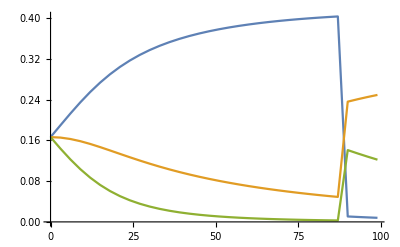

```mathematica
ListPlot[Table[{B,(CoeficientTable[gs1,SelectStates[es,M==0],B][[1,i,4]])^2},{i,3},{B,0,100,3}],Joined->True]
```

### Save parameters to file

#### Calculate parameters

```mathematica
ΔZground=4;
B=2*ΔZground;

Beff =Nearest[Bs,B][[1]];
```

```mathematica
{coeffTableF1MMM,coeffTableF1MM,coeffTableF1M, coeffTableF1,coeffTableF1P,coeffTableF1PP,coeffTableF1PPP} =(Function[coeffSeries,Select[coeffSeries, #[[1]]==B&][[1,2]]])/@{coeffSeriesF1MMM,coeffSeriesF1MM,coeffSeriesF1M, coeffSeriesF1,coeffSeriesF1P,coeffSeriesF1PP,coeffSeriesF1PPP} ;
{coeffTableF2MMM,coeffTableF2MM,coeffTableF2M, coeffTableF2,coeffTableF2P,coeffTableF2PP,coeffTableF2PPP} =(Function[coeffSeries,Select[coeffSeries, #[[1]]==B&][[1,2]]])/@{coeffSeriesF2MMM,coeffSeriesF2MM,coeffSeriesF2M, coeffSeriesF2,coeffSeriesF2P,coeffSeriesF2PP,coeffSeriesF2PPP} ;
```

```mathematica
tableFormat[table_]:=MapAt[If[#==0,#,Sign[#]DisplayForm@SqrtBox[Evaluate@Rationalize[#^2]]]&,table,{All,All}]

Grid[{
{{TableForm[tableFormat@coeffTableF1PPP,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs1,SelectStates[es,M==3]}}]]},
TableForm[tableFormat@coeffTableF1MMM,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs1,SelectStates[es,M==-3]}}]]},
{TableForm[tableFormat@coeffTableF1PP,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs1,SelectStates[es,M==2]}}]],
TableForm[tableFormat@coeffTableF1MM,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs1,SelectStates[es,M==-2]}}]]},
{TableForm[tableFormat@coeffTableF1P,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs1,SelectStates[es,M==1]}}]],
TableForm[tableFormat@coeffTableF1M,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs1,SelectStates[es,M==-1]}}]]},
{TableForm[tableFormat@coeffTableF1,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs1,SelectStates[es,M==0]}}]],SpanFromLeft}
}]

Grid[{
{{TableForm[tableFormat@coeffTableF2PPP,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs2,SelectStates[es,M==3]}}]]},
TableForm[tableFormat@coeffTableF2MMM,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs2,SelectStates[es,M==-3]}}]]},
{TableForm[tableFormat@coeffTableF2PP,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs2,SelectStates[es,M==2]}}]],
TableForm[tableFormat@coeffTableF2MM,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs2,SelectStates[es,M==-2]}}]]},
{TableForm[tableFormat@coeffTableF2P,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs2,SelectStates[es,M==1]}}]],
TableForm[tableFormat@coeffTableF2M,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs2,SelectStates[es,M==-1]}}]]},
{TableForm[tableFormat@coeffTableF2,TableHeadings->Table[Table[{F[i],M[i]},{i,states}],{states,{gs2,SelectStates[es,M==0]}}]],SpanFromLeft}
}]
```

{ | {3,3}
{1,1} | 0.
{1,0} | 0.
{1,-1} | 0.} |  | {3,-3}
{1,1} | 0.
{1,0} | 0.
{1,-1} | 0.
 | {3,2} | {2,2}
{1,1} | -√0.0000998911 | -√0.2499
{1,0} | 0. | 0.
{1,-1} | 0. | 0. |  | {3,-2} | {2,-2}
{1,1} | 0. | 0.
{1,0} | 0. | 0.
{1,-1} | -√0.0000998911 | -√0.2499
 | {3,1} | {2,1} | {1,1}
{1,1} | -√0.0000759775 | -√0.108244 | √0.225013
{1,0} | √0.0000840275 | √0.142055 | √0.191194
{1,-1} | 0. | 0. | 0. |  | {3,-1} | {2,-1} | {1,-1}
{1,1} | 0. | 0. | 0.
{1,0} | √0.0000759775 | √0.108244 | -√0.225013
{1,-1} | -√0.0000840275 | -√0.142055 | -√0.191194
 | {3,0} | {2,0} | {1,0} | {0,0}
{1,1} | √0.0000271035 | √0.031412 | -√0.157503 | √0.227724
{1,0} | -√0.000119817 | -√0.164882 | √0.00808008 | √0.160251
{1,-1} | √0.0000331523 | √0.0541435 | √0.252599 | √0.109891 |

{ | {3,3}
{2,2} | √(1/2)
{2,1} | 0.
{2,0} | 0.
{2,-1} | 0.
{2,-2} | 0.} |  | {3,-3}
{2,2} | 0.
{2,1} | 0.
{2,0} | 0.
{2,-1} | 0.
{2,-2} | √(1/2)
 | {3,2} | {2,2}
{2,2} | √0.160005 | -√0.173328
{2,1} | -√0.339895 | -√0.0767715
{2,0} | 0. | 0.
{2,-1} | 0. | 0.
{2,-2} | 0. | 0. |  | {3,-2} | {2,-2}
{2,2} | 0. | 0.
{2,1} | 0. | 0.
{2,0} | 0. | 0.
{2,-1} | -√0.326572 | √0.0900949
{2,-2} | √0.173328 | √0.160005
 | {3,1} | {2,1} | {1,1}
{2,2} | √0.0307389 | -√0.0789995 | √0.0569283
{2,1} | -√0.261113 | √0.0506831 | √0.0215372
{2,0} | √0.207988 | √0.120018 | √0.00532689
{2,-1} | 0. | 0. | 0.
{2,-2} | 0. | 0. | 0. |  | {3,-1} | {2,-1} | {1,-1}
{2,2} | 0. | 0. | 0.
{2,1} | 0. | 0. | 0.
{2,0} | √0.191996 | -√0.129219 | √0.0121184
{2,-1} | -√0.271771 | -√0.0332793 | √0.0282826
{2,-2} | √0.0360722 | √0.0872031 | √0.0433913
 | {3,0} | {2,0} | {1,0} | {0,0}
{2,2} | 0. | 0. | 0. | 0.
{2,1} | √0.09408 | -√0.123655 | √0.0315035 | -√0.000761651
{2,0} | -√0.299663 | √0.000664467 | √0.0321595 | -√0.0008462
{2,-1} | √0.106077 | √0.125243 | √0.0181543 | -√0.000526077
{2,-2} | 0. | 0. | 0. | 0. |

#### Assign parameters to variables

```mathematica
(* Assign Subscript[A, ij] values |F=1,mF> -> |F={1,2},mF> *)
{{na},{na},{na}}=coeffTableF1MMM;
{{na,na},{na,na},{CGg1Mx3MM,CGg1Mx2MM}}=coeffTableF1MM;
{{na,na,na},{CGg1x3M,CGg1x2M,CGg1x1M},{CGg1Mx3M,CGg1Mx2M,CGg1Mx1M}}=coeffTableF1M;
{{CGg1Px3,CGg1Px2,CGg1Px1,CGg1Px0},{CGg1x3,CGg1x2,CGg1x1,CGg1x0},{CGg1Mx3,CGg1Mx2,CGg1Mx1,CGg1Mx0}}=coeffTableF1;
{{CGg1Px3P,CGg1Px2P,CGg1Px1P},{CGg1x3P,CGg1x2P,CGg1x1P},{na,na,na}}=coeffTableF1P;
{{CGg1Px3PP,CGg1Px2PP},{na,na},{na,na}}=coeffTableF1PP;
{{na},{na},{na}}=coeffTableF1PPP;

(* Assign Subscript[A, ij] values |F=2,mF> -> |F={1,2},mF> *)
{{na},{na},{na},{na},{CGg2MMx3MMM}}=coeffTableF2MMM;
{{na,na},{na,na},{na,na},{CGg2Mx3MM,CGg2Mx2MM},{CGg2MMx3MM,CGg2MMx2MM}}=  coeffTableF2MM;
{{na,na,na},{na,na,na},{CGg2x3M,CGg2x2M,CGg2x1M},{CGg2Mx3M,CGg2Mx2M,CGg2Mx1M},{CGg2MMx3M,CGg2MMx2M,CGg2MMx1M}}=coeffTableF2M;
{{na,na,na,na},{CGg2Px3,CGg2Px2,CGg2Px1,CGg2Px0},{CGg2x3,CGg2x2,CGg2x1,CGg2x0},{CGg2Mx3,CGg2Mx2,CGg2Mx1,CGg2Mx0},{na,na,na,na}}=coeffTableF2;
{{CGg2PPx3P,CGg2PPx2P,CGg2PPx1P},{CGg2Px3P,CGg2Px2P,CGg2Px1P},{CGg2x3P,CGg2x2P,CGg2x1P},{na,na,na},{na,na,na}}=coeffTableF2P;
{{CGg2PPx3PP,CGg2PPx2PP},{CGg2Px3PP,CGg2Px2PP},{na,na},{na,na},{na,na}}=coeffTableF2PP;
{{CGg2PPx3PPP},{na},{na},{na},{na}}=coeffTableF2PPP;
```

```mathematica
(* Assign ΔZi values *)
energyTableZero=EnergyLevels[SelectStates[es,M==0],0]
 {energyTableMMM,energyTableMM,energyTableM, energyTable,energyTableP,energyTablePP,energyTablePPP} =EnergyLevels[SelectStates[es,M==#],B]&/@{-3,-2,-1,0,1,2,3}

{ΔZx3MMM}=energyTableMMM[[1]]-energyTableZero[[1]][[;;1]];
{ΔZx3MM, ΔZx2MM}=energyTableMM[[1]]-energyTableZero[[1]][[;;2]];
{ΔZx3M, ΔZx2M,ΔZx1M}=energyTableM[[1]]-energyTableZero[[1]][[;;3]] ;
{ΔZx3, ΔZx2,ΔZx1, ΔZx0}=energyTable[[1]]-energyTableZero[[1]];
{ΔZx3P, ΔZx2P,ΔZx1P}=energyTableP[[1]]-energyTableZero[[1]][[;;3]] ;
{ΔZx3PP, ΔZx2PP}=energyTablePP[[1]]-energyTableZero[[1]][[;;2]] ;
{ΔZx3PPP}=energyTablePPP[[1]]-energyTableZero[[1]][[;;1]] ;

ΔEx3 = #[[1]]-#[[2]]&@energyTableZero[[1]];
ΔEx1 = #[[3]]-#[[2]]&@energyTableZero[[1]];
ΔEx0 = #[[4]]-#[[2]]&@energyTableZero[[1]];
{ΔEx3,ΔEx1,ΔEx0}
ΔZ = EnergyLevels[SelectStates[gs2,M==1],B][[1,1]] - EnergyLevels[SelectStates[gs2,M==1],0][[1,1]]
```

{3,0} | 495.814
{2,0} | 229.163
{1,0} | 72.222
{0,0} | 0.

{{3,-3} | 479.814,{3,-2} | 485.254
{2,-2} | 218.389,{3,-1} | 490.652
{2,-1} | 224.093
{1,-1} | 66.4546,{3,0} | 496.007
{2,0} | 229.551
{1,0} | 73.5697
{0,0} | -1.92827,{3,1} | 501.319
{2,1} | 234.759
{1,1} | 77.1213,{3,2} | 506.588
{2,2} | 239.723,{3,3} | 511.814}

{266.652,-156.941,-229.163}

4

#### Save to file

```mathematica
CGsg1=Transpose[{
{"CGg1Mx3MM","CGg1Mx2MM",
"CGg1x3M","CGg1x2M","CGg1x1M","CGg1Mx3M","CGg1Mx2M","CGg1Mx1M",
"CGg1Px3","CGg1Px2","CGg1Px1","CGg1Px0","CGg1x3","CGg1x2","CGg1x1","CGg1x0","CGg1Mx3","CGg1Mx2","CGg1Mx1","CGg1Mx0",
"CGg1Px3P","CGg1Px2P","CGg1Px1P","CGg1x3P","CGg1x2P","CGg1x1P",
"CGg1Px3PP","CGg1Px2PP"},
{CGg1Mx3MM,CGg1Mx2MM,
CGg1x3M,CGg1x2M,CGg1x1M,CGg1Mx3M,CGg1Mx2M,CGg1Mx1M,
CGg1Px3,CGg1Px2,CGg1Px1,CGg1Px0,CGg1x3,CGg1x2,CGg1x1,CGg1x0,CGg1Mx3,CGg1Mx2,CGg1Mx1,CGg1Mx0,
CGg1Px3P,CGg1Px2P,CGg1Px1P,CGg1x3P,CGg1x2P,CGg1x1P,
CGg1Px3PP,CGg1Px2PP}
}];
CGsg2=Transpose[{
{"CGg2MMx3MMM",
"CGg2Mx3MM","CGg2Mx2MM","CGg2MMx3MM","CGg2MMx2MM",
"CGg2x3M","CGg2x2M","CGg2x1M","CGg2Mx3M","CGg2Mx2M","CGg2Mx1M","CGg2MMx3M","CGg2MMx2M","CGg2MMx1M",
"CGg2Px3","CGg2Px2","CGg2Px1","CGg2Px0","CGg2x3","CGg2x2","CGg2x1","CGg2x0","CGg2Mx3","CGg2Mx2","CGg2Mx1","CGg2Mx0",
"CGg2PPx3P","CGg2PPx2P","CGg2PPx1P","CGg2Px3P","CGg2Px2P","CGg2Px1P","CGg2x3P","CGg2x2P","CGg2x1P",
"CGg2PPx3PP","CGg2PPx2PP","CGg2Px3PP","CGg2Px2PP",
"CGg2PPx3PPP"},
{CGg2MMx3MMM,
CGg2Mx3MM,CGg2Mx2MM,CGg2MMx3MM,CGg2MMx2MM,
CGg2x3M,CGg2x2M,CGg2x1M,CGg2Mx3M,CGg2Mx2M,CGg2Mx1M,CGg2MMx3M,CGg2MMx2M,CGg2MMx1M,
CGg2Px3,CGg2Px2,CGg2Px1,CGg2Px0,CGg2x3,CGg2x2,CGg2x1,CGg2x0,CGg2Mx3,CGg2Mx2,CGg2Mx1,CGg2Mx0,
CGg2PPx3P,CGg2PPx2P,CGg2PPx1P,CGg2Px3P,CGg2Px2P,CGg2Px1P,CGg2x3P,CGg2x2P,CGg2x1P,
CGg2PPx3PP,CGg2PPx2PP,CGg2Px3PP,CGg2Px2PP,
CGg2PPx3PPP}
}];

deltas=Transpose[{{"deltaZ","deltaEx3","deltaEx1","deltaEx0",
"deltaZx3MMM",
"deltaZx3MM","deltaZx2MM",
"deltaZx3M","deltaZx2M","deltaZx1M",
"deltaZx3","deltaZx2","deltaZx1","deltaZx0",
"deltaZx3P","deltaZx2P","deltaZx1P",
"deltaZx3PP","deltaZx2PP",
"deltaZx3PPP"},
{ΔZ,ΔEx3,ΔEx1,ΔEx0,
ΔZx3MMM,
ΔZx3MM,ΔZx2MM,
ΔZx3M,ΔZx2M,ΔZx1M,
ΔZx3,ΔZx2,ΔZx1,ΔZx0,
ΔZx3P,ΔZx2P,ΔZx1P,
ΔZx3PP,ΔZx2PP,
ΔZx3PPP}
}];
data = {CGsg1,CGsg2,deltas};
data//TableForm
```

CGg1Mx3MM
-0.00999456 | CGg1Mx2MM
-0.4999 | CGg1x3M
0.00871651 | CGg1x2M
0.329004 | CGg1x1M
-0.474356 | CGg1Mx3M
-0.00916665 | CGg1Mx2M
-0.376902 | CGg1Mx1M
-0.437258 | CGg1Px3
0.00520611 | CGg1Px2
0.177234 | CGg1Px1
-0.396867 | CGg1Px0
0.477205 | CGg1x3
-0.0109461 | CGg1x2
-0.406057 | CGg1x1
0.0898893 | CGg1x0
0.400314 | CGg1Mx3
0.00575781 | CGg1Mx2
0.232688 | CGg1Mx1
0.502593 | CGg1Mx0
0.331497 | CGg1Px3P
-0.00871651 | CGg1Px2P
-0.329004 | CGg1Px1P
0.474356 | CGg1x3P
0.00916665 | CGg1x2P
0.376902 | CGg1x1P
0.437258 | CGg1Px3PP
-0.00999456 | CGg1Px2PP
-0.4999 |  |  |  |  |  |  |  |  |  |  |  | 
CGg2MMx3MMM
0.707107 | CGg2Mx3MM
-0.571465 | CGg2Mx2MM
0.300158 | CGg2MMx3MM
0.416327 | CGg2MMx2MM
0.400006 | CGg2x3M
0.438174 | CGg2x2M
-0.35947 | CGg2x1M
0.110084 | CGg2Mx3M
-0.521317 | CGg2Mx2M
-0.182426 | CGg2Mx1M
0.168174 | CGg2MMx3M
0.189927 | CGg2MMx2M
0.295302 | CGg2MMx1M
0.208306 | CGg2Px3
0.306725 | CGg2Px2
-0.351646 | CGg2Px1
0.177492 | CGg2Px0
-0.027598 | CGg2x3
-0.547415 | CGg2x2
0.0257773 | CGg2x1
0.179331 | CGg2x0
-0.0290895 | CGg2Mx3
0.325694 | CGg2Mx2
0.353897 | CGg2Mx1
0.134738 | CGg2Mx0
-0.0229364 | CGg2PPx3P
0.175325 | CGg2PPx2P
-0.281068 | CGg2PPx1P
0.238596 | CGg2Px3P
-0.510992 | CGg2Px2P
0.225129 | CGg2Px1P
0.146756 | CGg2x3P
0.456057 | CGg2x2P
0.346437 | CGg2x1P
0.0729855 | CGg2PPx3PP
0.400006 | CGg2PPx2PP
-0.416327 | CGg2Px3PP
-0.583005 | CGg2Px2PP
-0.277077 | CGg2PPx3PPP
0.707107
deltaZ
4 | deltaEx3
266.652 | deltaEx1
-156.941 | deltaEx0
-229.163 | deltaZx3MMM
-16. | deltaZx3MM
-10.56 | deltaZx2MM
-10.7733 | deltaZx3M
-5.16266 | deltaZx2M
-5.06992 | deltaZx1M
-5.76741 | deltaZx3
0.192027 | deltaZx2
0.388543 | deltaZx1
1.3477 | deltaZx0
-1.92827 | deltaZx3P
5.504 | deltaZx2P
5.59674 | deltaZx1P
4.89925 | deltaZx3PP
10.7733 | deltaZx2PP
10.56 | deltaZx3PPP
16. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
Export[NotebookDirectory[]<>"../params/exp_params_"<>StringReplace[ToString[Abs@ΔZ],"."->"p"]<>"MHz.csv",Flatten[data,1], "TextDelimiters"-> None]
```

/Users/tombarrett/PycharmProjects/Rb CQED/Rb CQED_Zeeman Scheme/Mathematica/../params/exp_params_4MHz.csv